# Iteration 1: SZR Model

## Basic Model

### Parameters

S → Susceptible Humans
Z → Zombies
R → Removed
β_z → Infection Rate
α_z → Zombie Removal Rate
μ → Human Removal Rate

### Differential Equations

S^I = - β_zSZ - μS
Z^I = β_zSZ - α_zZ
R^I = α_zZ + μS

### Non-Dimensional Equations

S^I = - R_0SZ
Z^I = R_0SZ - Z
R^I = Z + S

R_0 → Basic Reproduction Rate

```mathematica
Manipulate[
 Module[
  {
   eqns, sol, S, Z, R, t, Sf, Zf, Rf, ppSZ, ppZR, jMatrix, paramSpace, detJ, DJ, TJ, finalTJ
  },
  
  (* Non-Dimensionalised Equations, B0 = R0 = Basic Reproduction Rate *)
  eqns = {
    S'[t] == - B0 S[t] Z[t],
    Z'[t] == B0 S[t] Z[t] - Z[t],
    R'[t] == Z[t]
  };
  
  jMatrix = {
   {- B0 Z, - B0 S, 0},
   { B0 Z, (B0 S - 1), 0},
   {0, 1, 0}
	};
  paramSpace = ParametricPlot[{{d,0},{0,t},{t^2/4,t}},{d,-10,10},{t,-10,10},PlotRange->{{-10,10},{-10,10}}];
  (* Solving Equations *)
  sol = NDSolve[
    {eqns, 
     S[0] == S0/S0, 
     Z[0] == Z0/S0, 
     R[0] == R0/S0
    }, 
    {S, Z, R}, 
    {t, 0, tmax}
  ];
  
  (* Extracting Functions from Solutions *)
  Sf = S /. sol[[1]];
  Zf = Z /. sol[[1]];
  Rf = R /. sol[[1]];
  
  TJ = Tr[jMatrix];
  detJ = Det[jMatrix];
  finalTJ = TJ /. {S -> (S[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), B0 -> B0 };
  DJ = detJ /. {S -> (S[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), B0 -> B0 };
  
  (* Phase Stream Plots *)
  ppSZ = 
   StreamPlot[
    Evaluate[{
      - B0 S Z, 
     B0 S Z - Z
    }],
    {S, 0, 1}, {Z, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"Susceptible Humans (S)", "Zombies (Z)"},
    Frame -> True,
    FrameLabel -> {"Susceptible Humans (S)", "Zombies (Z)"}
   ];
   ppZR = 
   StreamPlot[
    Evaluate[{
      B0 S Z - Z,
      Z
    } /. {S -> Sf[tmax]}],
    {Z, 0, 1}, {R, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"Zombies (Z)", "Removed (R)"},
    Frame -> True,
    FrameLabel -> {"Zombies (Z)", "Removed (R)"}
   ];
  
  (* Show Results *)
  detTracePlot =
  Show[
    paramSpace,
    ListPlot[{{DJ, finalTJ}}, PlotStyle -> PointSize[Large]],
    Frame -> True,
    FrameLabel -> {"Determinant", "Trace"}
  ];
  
  Row[{
    Plot[
     {Sf[t], Zf[t], Rf[t]}, {t, 0, tmax},
     ImageSize -> 400,
     PlotRange -> All,
     PlotLegends -> {"S", "Z", "R"},
     PlotStyle -> {{Green, Thick}, {Blue, Thick}, {GrayLevel[0.677], Thick}},
     AxesLabel -> {"Time (t)", "Population"},
     Frame -> True,
     FrameLabel -> {"Time (t)", "Population Fractions"}
    ],
    ppSZ/. Graphics[g_, opts___] :> Graphics[g, ImageSize -> 400, opts],
    ppZR/. Graphics[g_, opts___] :> Graphics[g, ImageSize -> 400, opts],
    Show[Show[detTracePlot, ImageSize -> 600]
	]
   }]
 ],
 
 (* Sliders *)
 {{B0, 1, "Basic Reproduction Rate "}, 0, 2, 0.01},
 {{S0, 650, "Initial No. of Susceptible Humans"}, 0, 1000, 1},
 {{Z0, 350, "Initial No. of Zombies"}, 0, 1000, 1},
 {{R0, 0, "Initial No. of Removed"}, 0, 1000, 1},
 {{tmax, 10, "Simulation Time"}, 0, 1000, 1}
]
```

## Eigen Analysis + Bifurication

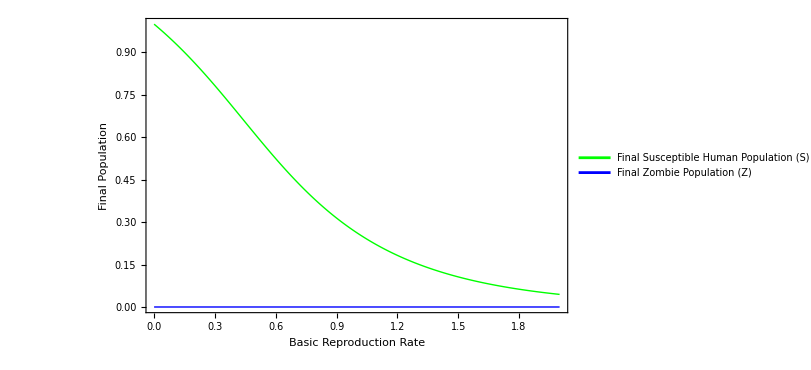

```mathematica
(* Jacobian Matrix *)
jMatrix = {
   {-R0 Z, -R0 S, 0},
   { R0 Z,  R0 S - 1, 0},
   {0, 1, 0}
};

FP1 = {Z -> 0};
FP2 = {S -> 0, Z -> 0};

eVals  = Eigenvalues[jMatrix];
eVects = Eigenvectors[jMatrix];

eV1 = Eigenvalues[jMatrix /. FP1];
eV2 = Eigenvalues[jMatrix /. FP2];

(* S and Z with changing R0 *)
final = Table[
  Module[{sol, Sfunc, Zfunc, finalS, finalZ, eqns},
    
    eqns = {
      S'[t] == -R0 S[t] Z[t],
      Z'[t] ==  R0 S[t] Z[t] - Z[t],
      R'[t] ==  Z[t]
    };
    
    sol = NDSolve[
      {
        eqns,
        S[0] == 500/500,
        Z[0] == 300/500,
        R[0] == 0/500
      },
      {S, Z, R},
      {t, 0, 10000}
    ];
    
    Sfunc = S /. sol[[1]];
    Zfunc = Z /. sol[[1]];
    
    finalS = Sfunc[10000];
    finalZ = Zfunc[10000];
    
    {R0, finalS, finalZ}
  ],
  {R0, 0, 2, 0.01}
];

varR0 = final[[All, 1]];
finalSv  = final[[All, 2]];
finalZv  = final[[All, 3]];

ListLinePlot[
  {
    Transpose[{varR0, finalSv}],
    Transpose[{varR0, finalZv}]
  },
  PlotRange   -> All,
  PlotLegends -> {"Final Susceptible Human Population (S)", "Final Zombie Population (Z)"},
  PlotStyle   -> {{Green, Thick}, {Blue, Thick}},
  AxesLabel   -> {"Basic Reproduction Number (R0)", "Final Population"},
  Frame       -> True,
  FrameLabel  -> {"Basic Reproduction Rate", "Final Population"},
  ImageSize -> 600
]
```